3/4 (-2 (-1+Cot[π/18]^2) Sinh[r]^2 (3+5 Sinh[r]^2)+Csc[π/18]^2 Sinh[2 r])

1+3 Sinh[r]^2

15 Cosh[r]^2 Sinh[r]^2

3/4 (-2 (-1+Cot[π/18]^2) Sinh[r]^2 (3+5 Sinh[r]^2)+Csc[π/18]^2 Sinh[2 r])

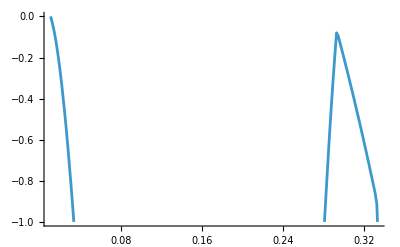

```mathematica
ClearAll;
ClearAll["`*", Subscript, Derivative];
ClearAll["Global`*",Derivative,Subscript];
β= (-s )(Cosh[r]-ⅇ^(ⅈ θ) Sinh[r]);
NN=1/(√2)(1+Abs[A]^2+ (1-Abs[A]^2)(1-Abs[β]^2 )ⅇ^(-1/2  Abs[β]^2) )^(-1/2);
(*-Graphics- FOR INTIAL STATE *)
(*<a^+a>*)
H1=2 Abs[NN]^2((  1+ Abs[A]^2 )(1+3 Sinh[r]^2+s^2/4)+(1-Abs[A]^2)Subscript[P, 1] );
Subscript[P, 1]=Subscript[R, 5]+s Subscript[R, 6]+s/2(Subscript[R, 6]+s Subscript[R, 7]+Subscript[R, 1]+s Subscript[R, 2])+s^2/4 Subscript[R, 3];
Subscript[R, 1]=( β Cosh[r]( β^2 ⅇ^(-ⅈ θ) Coth[r]+3 ))ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 2]=(β^2 ⅇ^(-ⅈ θ) Coth[r]+1)ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 3]=(1-Abs[β]^2 )ⅇ^(-1/2  Abs[β]^2);
Subscript[R, 4]=(β^2 Cosh[r]^2( β^2 ⅇ^(-ⅈ θ)Coth[r]+6 )+3/2 ⅇ^(ⅈ θ)Sinh[2r])ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 5]=(β^2 ⅇ^(-ⅈ θ) Cosh[r](Coth[r]Cosh[r]+5Sinh[r]+β^2 ⅇ^(-ⅈ θ)Cosh[r]) +1+3 Sinh[r]^2 )ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 6]=β ⅇ^(-ⅈ θ) ( (1+3 Sinh[r]^2)/Sinh[r]+β^2 ⅇ^(-ⅈ θ)Cosh[r] )ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 7]=ⅇ^(-ⅈ θ)(Coth[r]+β^2 ⅇ^(-ⅈ θ))ⅇ^(-1/2 Abs[β]^2);
(*-Graphics-FOR INTIAL STATE*)
(* <Φ | a^(+2)a^2 |Φ> *)
H2= 2 Abs[NN]^2( (1+ Abs[A]^2 )Subscript[P, 2]+ (1-Abs[A]^2)Subscript[P, 3] );
Subscript[P, 2]=3 Sinh[r]^2(3+5 Sinh[r]^2)+s^2/2(3/2 Cos[θ] Sinh[2 r]+2(1+3 Sinh[r]^2) )+s^4/16;
Subscript[P, 3]=Subscript[J, 1]+s (Subscript[J, 2]+Subscript[J, 3])+s^2/4(Subscript[J, 4]+Subscript[J, 5]+4 Subscript[J, 6])+s^3/4(Subscript[J, 7]+Subscript[J, 8])+s^4/16 Subscript[R, 3];
Subscript[J, 1]=Subscript[K, 1]+s Subscript[K, 2] ;
Subscript[J, 2]=Subscript[K, 2]+s Subscript[K, 3];
Subscript[J, 3]=Subscript[K, 4]+s Subscript[R, 5];
Subscript[J, 4]=Subscript[K, 3]+s Subscript[K, 5];
Subscript[J, 5]=Subscript[R, 4]+s Subscript[R, 1];
Subscript[J, 6]=Subscript[R, 5]+s Subscript[R, 6] ;
Subscript[J, 7]=Subscript[R, 6]+s Subscript[R, 7];
Subscript[J, 8]=Subscript[R, 1]+s Subscript[R, 2];
Subscript[K, 1]= ( β^6 ⅇ^(-3ⅈ θ)Sinh[r] Cosh[r]^3+3 β^4 ⅇ^(-2ⅈ θ)Cosh[r]^2( 1+5 Sinh[r]^2 )+9/2 β^2 Sinh[2 r] ⅇ^(-ⅈ θ)(2+ 3 Sinh[r]^2)+3 Sinh[r]^2(3+5 Sinh[r]^2) )ⅇ^(-1/2 Abs[β]^2);
Subscript[K, 2]=  ( β^5 ⅇ^(-3 ⅈ θ)Sinh[r] Cosh[r]^2+β^3 ⅇ^(-2ⅈ θ)Cosh[r](3+10 Sinh[r]^2)+3β ⅇ^(-ⅈ θ)Sinh[r](3+5 Sinh[r]^2))ⅇ^(-1/2 Abs[β]^2);
Subscript[K, 3]= ( 1/2 β^4 ⅇ^(-3 ⅈ θ)Sinh[2r] +3 β^2 ⅇ^(-2 ⅈ θ) Cosh[2r]+3/2 ⅇ^(-ⅈ θ)Sinh[2r] ) ⅇ^(-1/2 Abs[β]^2);
Subscript[K, 4]= (β^5 ⅇ^(-2ⅈ θ)Cosh[r]^3+β^3 ⅇ^(-ⅈ θ)Cosh[r]^2(Cosh[r]Coth[r] +9Sinh[r] )+3β Cosh[r]( 1+5 Sinh[r]^2 ) ) ⅇ^(-1/2 Abs[β]^2);
Subscript[K, 5]=  (β ⅇ^(-2ⅈ θ)(β^2 ⅇ^(-ⅈ θ)Sinh[r] +3Cosh[r]))ⅇ^(-1/2 Abs[β]^2) ;
(*-Graphics-*)
(*<a^2>*)
H4=2 Abs[NN]^2((1+ Abs[A]^2 )(3/2 ⅇ^(ⅈ θ) Sinh[2r]+s^2/4)+(1-Abs[A]^2)Subscript[P, 2] );
Subscript[P, 2]=Subscript[R, 4]+s Subscript[R, 1]+s(Subscript[R, 1]+s Subscript[R, 2])+s^2/4 Subscript[R, 3];
Subscript[R, 1]=( β Cosh[r]( β^2 ⅇ^(-ⅈ θ) Coth[r]+3 ))ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 2]=(β^2 ⅇ^(-ⅈ θ) Coth[r]+1)ⅇ^(-1/2 Abs[β]^2);
Subscript[R, 3]=(1-Abs[β]^2 )ⅇ^(-1/2  Abs[β]^2);
Subscript[R, 4]=(β^2 Cosh[r]^2( β^2 ⅇ^(-ⅈ θ)Coth[r]+6 )+3/2 ⅇ^(ⅈ θ)Sinh[2r])ⅇ^(-1/2 Abs[β]^2);
(*-Graphics-*)
H3=2 Abs[NN]^2((1+ Abs[A]^2 )Subscript[V, 1]+(1- Abs[A]^2 )Subscript[V, 2]);
Subscript[V, 1]=15 ⅇ^(2ⅈ θ)Sinh[r]^2 Cosh[r]^2+9 s^2/2 ⅇ^(ⅈ θ)Sinh[r]Cosh[r]+s^4/16;
Subscript[V, 2]=Subscript[Z, 2]+s Subscript[Z, 1]+2s(Subscript[Z, 1]+s Subscript[R, 4])+(3 s^2)/2(Subscript[R, 4]+s Subscript[R, 1])+s^3/2(Subscript[R, 1]+s Subscript[R, 2])+s^4/16 Subscript[R, 3];
Subscript[Z, 1]=(β^5 ⅇ^(-ⅈ θ)Coth[r] Cosh[r]^3+10 β^3 Cosh[r]^3+15β ⅇ^(-ⅈ θ) Sinh[r]^2 Cosh[r]^2)ⅇ^(-1/2 Abs[β]^2);
Subscript[Z, 2]=(β^6 Cosh[r]^4 Coth[r]+15 ⅇ^(2ⅈ θ)Cosh[r]^2 Sinh[r]^2)ⅇ^(-1/2 Abs[β]^2);
(*-Graphics-g=H2/(H1)^2;QM=H1 (g -1);*)
(*-Graphics-*)
AS=(1/2(H2-Abs[H4]^2-Abs[H3-(H4)^2]))/(H1+1/2);
A=ⅇ^(ⅈ δ) Tan[α/2];
δ=0;
θ=0 ;
α=(8π)/9;
s=0;
FullSimplify[H2]
FullSimplify[H1]
FullSimplify[H3]
FullSimplify[H4]
Plot[AS,{r,0,5},PlotRange->{0,-1}]
```